```mathematica
Plus@@{1,2,3}
```

6

```mathematica
h/@{x1,x2,x3}
```

{h[x1],h[x2],h[x3]}

```mathematica
h@@{x1,x2,x3}
```

h[x1,x2,x3]

```mathematica
h[(Sequence@@Range[10])]
```

h[1,2,3,4,5,6,7,8,9,10]

```mathematica
{x1,x2,x3}//h
```

h[{x1,x2,x3}]

```mathematica
Sequence[x1,x2,x3]//h
```

h[x1,x2,x3]

```mathematica
Sequence@@{x1,x2,x3}//h
```

h[x1,x2,x3]

```mathematica
Head[1.1]
```

Real

```mathematica
List@@h@@{x1,x2,x3}
```

{x1,x2,x3}

```mathematica
Sequence@@h@@{x1,x2,x3}
```

Sequence[x1,x2,x3]

```mathematica
g@@h@@{x1,x2,x3}
```

g[x1,x2,x3]

Sequence[1,2,3,4,5,6,7,8,9,10]

```mathematica
{x1,x2,x3}[[1;;2]]
```

{x1,x2}

```mathematica
Range[10][[1;;3;;2]]
```

{1,3}

```mathematica
eq = f[g[x1,h[x1,x2]],x4];
```

2

4

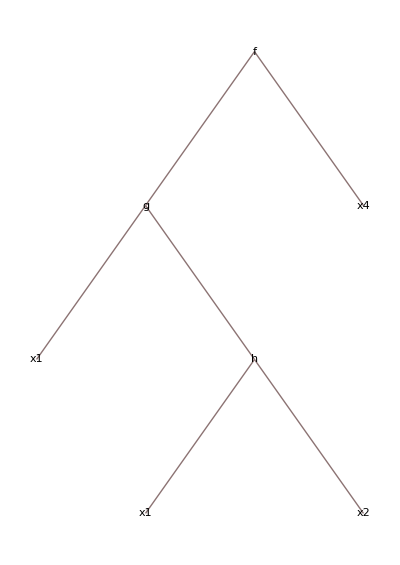

```mathematica
Length[eq](* the number of children of root *)
Depth[eq](* the number of levels *)
TreeForm[eq]
```

## Construct Tables

```mathematica
Range[2,10]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Table[i^2+i+1,{i,10}]
```

{3,7,13,21,31,43,57,73,91,111}

```mathematica
Array[#^2+#+1&,10] (* no need for declaration*)
```

{3,7,13,21,31,43,57,73,91,111}

```mathematica
Array[f,5,2,h]
```

h[f[2],f[3],f[4],f[5],f[6]]

```mathematica
Tuples[Range[3],3]//MatrixForm
```

(1 | 1 | 1
1 | 1 | 2
1 | 1 | 3
1 | 2 | 1
1 | 2 | 2
1 | 2 | 3
1 | 3 | 1
1 | 3 | 2
1 | 3 | 3
2 | 1 | 1
2 | 1 | 2
2 | 1 | 3
2 | 2 | 1
2 | 2 | 2
2 | 2 | 3
2 | 3 | 1
2 | 3 | 2
2 | 3 | 3
3 | 1 | 1
3 | 1 | 2
3 | 1 | 3
3 | 2 | 1
3 | 2 | 2
3 | 2 | 3
3 | 3 | 1
3 | 3 | 2
3 | 3 | 3)

```mathematica
Outer[f,Range[3],Range[2]]//MatrixForm
```

(f[1,1] | f[1,2]
f[2,1] | f[2,2]
f[3,1] | f[3,2])

-Graphics-

```mathematica
RotateLeft[%]
```

RotateLeft::normal: Nonatomic expression expected at position 1 in ….

RotateLeft[-Graphics-]

```mathematica
Rotate[-Graphics-,30 Degree]
```

-Graphics-

## Reap & Sow